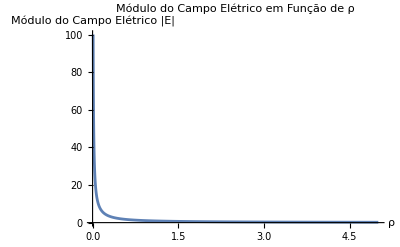

```mathematica
(*Questão 1a)*)
λ0=1;  (*Densidade linear constante*)
ε0=8.854187817620389*^-12;  (*Permissividade do vácuo, não será utilizado pois (2 π ε0)=1*)

(*Defina a expressão do módulo do campo elétrico vezes ρ*)
Efield[ρ_]=(1/(1λ0 ρ));

(*Crie um gráfico do módulo do campo elétrico em função de ρ*)
Plot[Efield[ρ],{ρ,0.01,5},AxesLabel->{"ρ","Módulo do Campo Elétrico |E|"},PlotLabel->"Módulo do Campo Elétrico em Função de ρ",PlotRange->All]
```

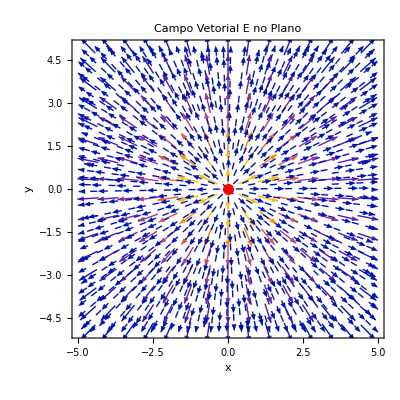

```mathematica
(*Questão 1b) *)
λ0=1;  (*Densidade linear constante*)
ε0=8.854187817620389*^-12;  (*Permissividade do vácuo, não será utilizado pois (2 π ε0)=1*)

(*Expressão do campo elétrico em coordenadas cartesianas*)
Ex[x_,y_]=(λ0/(1x^2+y^2)) x;
Ey[x_,y_]=(λ0/(1x^2+y^2)) y;

(*Gráfico do campo vetorial no plano*)
VectorPlot[{Ex[x,y],Ey[x,y]},{x,-5,5},{y,-5,5},VectorPoints->15,VectorScale->{0.05,Automatic,None},VectorStyle->Arrowheads[0.02],Epilog->{Red,PointSize[0.02],Point[{0,0}]},StreamPoints->Fine,StreamStyle->Directive[Gray,Dashed],FrameLabel->{"x","y"},PlotLabel->"Campo Vetorial E no Plano",ImageSize->400]
```

```mathematica
(*Questão 1c)*)
(*Expressão do campo elétrico em coordenadas cartesianas*)
Efield[x_,y_,z_]={x,y,z}/(x^2+y^2+z^2)^(3/2);

(*Gráfico do campo vetorial no espaço 3D*)
VectorPlot3D[Efield[x,y,z],{x,-5,5},{y,-5,5},{z,-5,5},
VectorPoints->15,
VectorScale->{0.1,Scaled[0.2],None}
,VectorStyle->Arrowheads[0.03],
Epilog->{Red,PointSize[0.03],Point[{0,0,0}]},
Boxed->False,AxesLabel->{"x","y","z"},
PlotLabel->"Campo Vetorial E no Espaço 3D",ImageSize->400]
```

-Graphics3D-

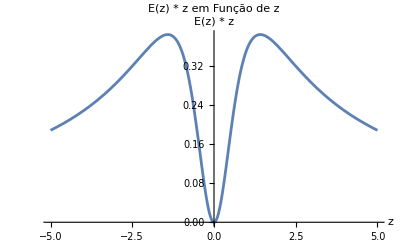

```mathematica
(*Questão 2a)*)
ε0=8.854187817620389*^-12;  (*Permissividade do vácuo, não será utilizado pois (4 π ε0)= 1*)
Q=1;  (*Carga total do anel*)
R=1;  (*Raio do anel*)

(*Defina a expressão do campo elétrico em função de z*)
Ez[z_]=(Q z)/(1(z^2+R^2)^(3/2));

(*Crie um gráfico de E(z)*z em função de z*)
Plot[Ez[z] z,{z,-5,5},AxesLabel->{"z","E(z) * z"},PlotLabel->"E(z) * z em Função de z",PlotRange->All]
```

```mathematica
(*Questão 2b)*)
ε0=8.854187817620389*^-12;  (*Permissividade do vácuo, não será utilizado pois (4 π ε0)= 1*)
Q=1;  (*Carga total do anel*)

(*Expressão do campo elétrico em função de z e R*)
EzR[z_,R_]=(Q z)/(1(z^2+R^2)^(3/2));

(*Gráfico tridimensional de E(z,R) em função de z e R*)
Plot3D[EzR[z,R],{z,-5,5},{R,0,5},AxesLabel->{"z","R","E(z, R)"},PlotLabel->"Campo Elétrico E(z, R) em Função de z e R"]
```

-Graphics3D-